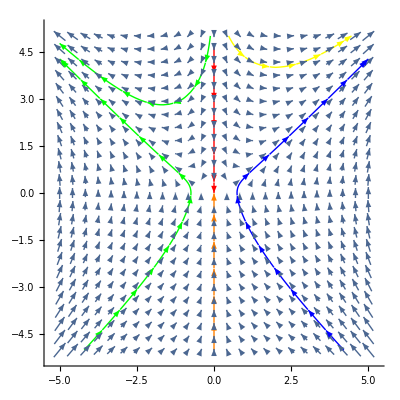

```mathematica
VectorPlot[{x*y,x^2-y},{x,-5,5},{y,-5,5},VectorScale->{Automatic},VectorStyle->Automatic,StreamStyle->Blue,StreamPoints->{{{{1,.5},Automatic},{{-1,3},Green},{{0,.5},Red},{{0,-1},Orange},{{-1,.5},Green},{{2,4},Yellow}}},Axes->True,Frame->None,VectorPoints->Fine]
```

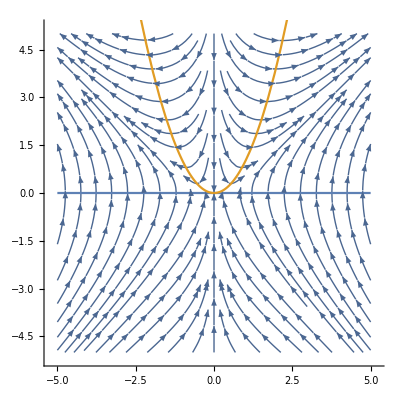

```mathematica
Show[StreamPlot[{x*y,x^2-y},{x,-5,5},{y,-5,5} ,StreamPoints->{{{{0,0},Red}, Automatic}},Axes->True,Frame->None],Plot[{0,x^2},{x,-5,5},AspectRatio->1]]
```

```mathematica
Eigensystem[{{0,0},{0,-1}}]
```

{{-1,0},{{0,1},{1,0}}}

```mathematica
Solve[e*u^2-u+a==0,u]
```

{{u→(1-√(1-4 a e))/(2 e)},{u→(1+√(1-4 a e))/(2 e)}}

```mathematica
Det[{{0,1},{2*e*(1-√(1-4 a e))/(2 e)-1,0}}]
```

√(1-4 a e)

```mathematica
Det[{{0,1},{2*e*(1+√(1-4 a e))/(2 e)-1,0}}]
```

-√(1-4 a e)

```mathematica
Eigensystem[{{0,1},{2*e*(1+√(1-4 a e))/(2 e),0}}]
```

{{-√(1+√(1-4 a e)),√(1+√(1-4 a e))},{{-1/(√(1+√(1-4 a e))),1},{1/(√(1+√(1-4 a e))),1}}}

```mathematica
Eigensystem[{{0,1},{2*e*(1-√(1-4 a e))/(2 e),0}}]
```

{{-√(1-√(1-4 a e)),√(1-√(1-4 a e))},{{-1/(√(1-√(1-4 a e))),1},{1/(√(1-√(1-4 a e))),1}}}

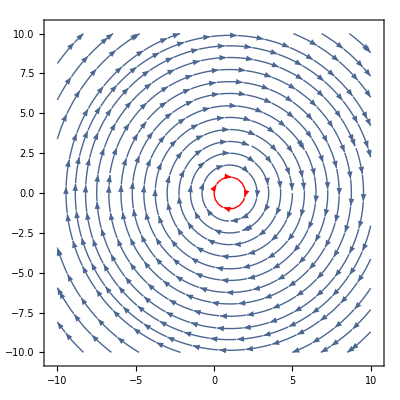

```mathematica
a=1;
e=0.001;
StreamPlot[{v,a+e*u^2-u},{u,-10,10},{v,-10,10},StreamPoints->{{{{1,1},Red}, Automatic}}]
```

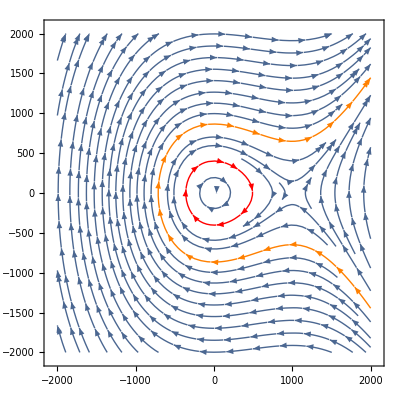

```mathematica
a=1;e=0.001;
StreamPlot[{v,a+e*u^2-u},{u,-2000,2000},{v,-2000,2000},StreamPoints->{{{{300,300},Red},{{700,700},Orange}, Automatic}}]
```

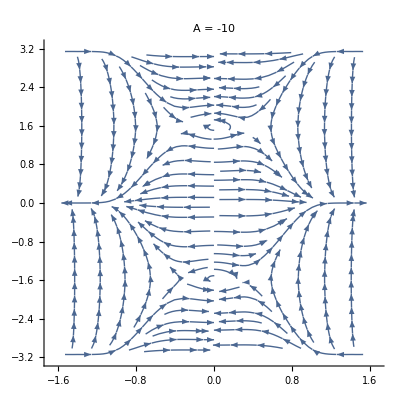
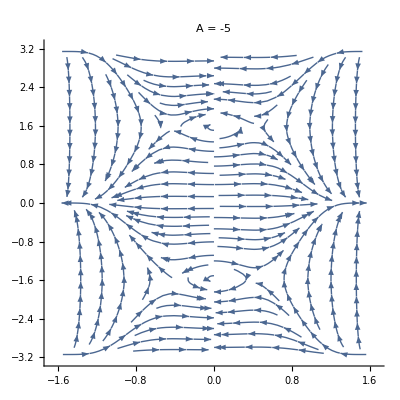
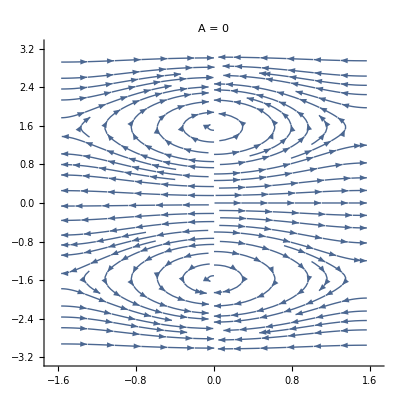
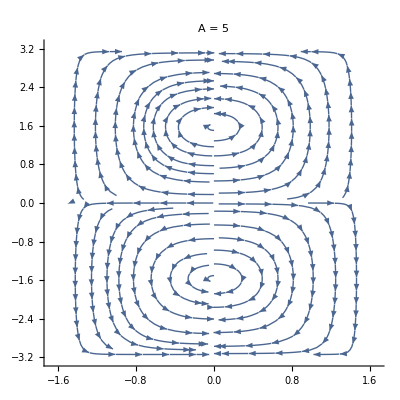
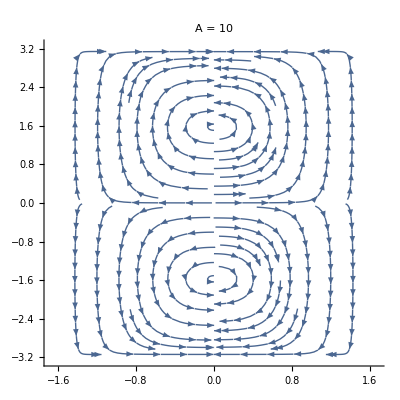

```mathematica
Clear[A];A=5;
Table[StreamPlot[{Cot[p]*Cos[t],((Cos[p])^2+A(Sin[p]^2))*Sin[t]},{p,-Pi/2,Pi/2},{t,-Pi,Pi} ,StreamPoints->{{{{0,0},Red}, Automatic}},Axes->True,Frame->None,PlotLabel->"A = " <> ToString[A]],{A,-10,10,5}]
```

```mathematica
ClearAll["Global`*"];A=-10;h=100;sol=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.1,t[0]==1.5},{p,t},{x,0,h}];
sola=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.1,t[0]==1.5},{p,t},{x,0,h}];
sol1=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.5,t[0]==0.5},{p,t},{x,0,h}];
sol1a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.5,t[0]==0.5},{p,t},{x,0,h}];
sol2=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==1},{p,t},{x,0,h}];
sol2a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==1},{p,t},{x,0,h}];
sol3=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==2.5},{p,t},{x,0,h}];
sol3a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==2.5},{p,t},{x,0,h}];
sol4=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1.25,t[0]==2.75},{p,t},{x,0,h}];
sol4a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1.25,t[0]==2.75},{p,t},{x,0,h}];
```

```mathematica
p = First[p/.sol];t=First[t/.sol];pa = First[p/.sola];ta=First[t/.sola];p1= First[p/.sol1];t1=First[t/.sol1];p1a= First[p/.sol1a];t1a=First[t/.sol1a];p2= First[p/.sol2];t2=First[t/.sol2];p2a= First[p/.sol2a];t2a=First[t/.sol2a];p3= First[p/.sol3];t3=First[t/.sol3];p3a= First[p/.sol3a];t3a=First[t/.sol3a];p4= First[p/.sol4];t4=First[t/.sol4];p4a= First[p/.sol4a];t4a=First[t/.sol4a];d=0.01;
sp[{r_,theta_,phi_}]:=r {Cos[phi] Cos[theta],Cos[phi] Sin[theta],Sin[phi]};
Show[Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t[x],p[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,ta[x],pa[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1[x],p1[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1a[x],p1a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2[x],p2[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2a[x],p2a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3[x],p3[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3a[x],p3a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4[x],p4[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4a[x],p4a[x]},{x,0,h,d}]]},AxesOrigin->{0,0,0},ViewPoint->Bottom,Boxed->False,PlotLabel->"A = " <> ToString[A]]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"];A=-5;h=100;sol=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.1,t[0]==1.5},{p,t},{x,0,h}];
sola=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.1,t[0]==1.5},{p,t},{x,0,h}];
sol1=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.5,t[0]==0.5},{p,t},{x,0,h}];
sol1a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.5,t[0]==0.5},{p,t},{x,0,h}];
sol2=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==1},{p,t},{x,0,h}];
sol2a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==1},{p,t},{x,0,h}];
sol3=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==2.5},{p,t},{x,0,h}];
sol3a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==2.5},{p,t},{x,0,h}];
sol4=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1.25,t[0]==2.75},{p,t},{x,0,h}];
sol4a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1.25,t[0]==2.75},{p,t},{x,0,h}];
```

```mathematica
p = First[p/.sol];t=First[t/.sol];pa = First[p/.sola];ta=First[t/.sola];p1= First[p/.sol1];t1=First[t/.sol1];p1a= First[p/.sol1a];t1a=First[t/.sol1a];p2= First[p/.sol2];t2=First[t/.sol2];p2a= First[p/.sol2a];t2a=First[t/.sol2a];p3= First[p/.sol3];t3=First[t/.sol3];p3a= First[p/.sol3a];t3a=First[t/.sol3a];p4= First[p/.sol4];t4=First[t/.sol4];p4a= First[p/.sol4a];t4a=First[t/.sol4a];d=0.01;
sp[{r_,theta_,phi_}]:=r {Cos[phi] Cos[theta],Cos[phi] Sin[theta],Sin[phi]};
Show[Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t[x],p[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,ta[x],pa[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1[x],p1[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1a[x],p1a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2[x],p2[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2a[x],p2a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3[x],p3[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3a[x],p3a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4[x],p4[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4a[x],p4a[x]},{x,0,h,d}]]},AxesOrigin->{0,0,0},ViewPoint->Bottom,Boxed->False,PlotLabel->"A = " <> ToString[A]]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"];A=0;h=100;sol=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.1,t[0]==1.5},{p,t},{x,0,h}];
sola=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.1,t[0]==1.5},{p,t},{x,0,h}];
sol1=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.5,t[0]==0.5},{p,t},{x,0,h}];
sol1a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.5,t[0]==0.5},{p,t},{x,0,h}];
sol2=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==1},{p,t},{x,0,h}];
sol2a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==1},{p,t},{x,0,h}];
sol3=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==2.5},{p,t},{x,0,h}];
sol3a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==2.5},{p,t},{x,0,h}];
sol4=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1.25,t[0]==2.75},{p,t},{x,0,h}];
sol4a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1.25,t[0]==2.75},{p,t},{x,0,h}];
```

```mathematica
p = First[p/.sol];t=First[t/.sol];pa = First[p/.sola];ta=First[t/.sola];p1= First[p/.sol1];t1=First[t/.sol1];p1a= First[p/.sol1a];t1a=First[t/.sol1a];p2= First[p/.sol2];t2=First[t/.sol2];p2a= First[p/.sol2a];t2a=First[t/.sol2a];p3= First[p/.sol3];t3=First[t/.sol3];p3a= First[p/.sol3a];t3a=First[t/.sol3a];p4= First[p/.sol4];t4=First[t/.sol4];p4a= First[p/.sol4a];t4a=First[t/.sol4a];d=0.1;
sp[{r_,theta_,phi_}]:=r {Cos[phi] Cos[theta],Cos[phi] Sin[theta],Sin[phi]};
Show[Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t[x],p[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,ta[x],pa[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1[x],p1[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1a[x],p1a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2[x],p2[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2a[x],p2a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3[x],p3[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3a[x],p3a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4[x],p4[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4a[x],p4a[x]},{x,0,h,d}]]},AxesOrigin->{0,0,0},ViewPoint->Bottom,Boxed->False,PlotLabel->"A = " <> ToString[A]]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"];A=5;h=100;sol=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.1,t[0]==1.5},{p,t},{x,0,h}];
sola=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.1,t[0]==1.5},{p,t},{x,0,h}];
sol1=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.5,t[0]==0.5},{p,t},{x,0,h}];
sol1a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.5,t[0]==0.5},{p,t},{x,0,h}];
sol2=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==1},{p,t},{x,0,h}];
sol2a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==1},{p,t},{x,0,h}];
sol3=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==2.5},{p,t},{x,0,h}];
sol3a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==2.5},{p,t},{x,0,h}];
sol4=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1.25,t[0]==2.75},{p,t},{x,0,h}];
sol4a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1.25,t[0]==2.75},{p,t},{x,0,h}];
```

```mathematica
p = First[p/.sol];t=First[t/.sol];pa = First[p/.sola];ta=First[t/.sola];p1= First[p/.sol1];t1=First[t/.sol1];p1a= First[p/.sol1a];t1a=First[t/.sol1a];p2= First[p/.sol2];t2=First[t/.sol2];p2a= First[p/.sol2a];t2a=First[t/.sol2a];p3= First[p/.sol3];t3=First[t/.sol3];p3a= First[p/.sol3a];t3a=First[t/.sol3a];p4= First[p/.sol4];t4=First[t/.sol4];p4a= First[p/.sol4a];t4a=First[t/.sol4a];d=0.1;
sp[{r_,theta_,phi_}]:=r {Cos[phi] Cos[theta],Cos[phi] Sin[theta],Sin[phi]};
Show[Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t[x],p[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,ta[x],pa[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1[x],p1[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1a[x],p1a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2[x],p2[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2a[x],p2a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3[x],p3[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3a[x],p3a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4[x],p4[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4a[x],p4a[x]},{x,0,h,d}]]},AxesOrigin->{0,0,0},ViewPoint->Bottom,Boxed->False,PlotLabel->"A = " <> ToString[A]]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"];A=10;h=100;sol=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.1,t[0]==1.5},{p,t},{x,0,h}];
sola=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.1,t[0]==1.5},{p,t},{x,0,h}];
sol1=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==0.5,t[0]==0.5},{p,t},{x,0,h}];
sol1a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-0.5,t[0]==0.5},{p,t},{x,0,h}];
sol2=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==1},{p,t},{x,0,h}];
sol2a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==1},{p,t},{x,0,h}];
sol3=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1,t[0]==2.5},{p,t},{x,0,h}];
sol3a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1,t[0]==2.5},{p,t},{x,0,h}];
sol4=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==1.25,t[0]==2.75},{p,t},{x,0,h}];
sol4a=NDSolve[{t'[x]==Cot[p[x]]*Cos[t[x]],p'[x]==((Cos[p[x]])^2+A(Sin[p[x]]^2))*Sin[t[x]],p[0]==-1.25,t[0]==2.75},{p,t},{x,0,h}];
```

```mathematica
p = First[p/.sol];t=First[t/.sol];pa = First[p/.sola];ta=First[t/.sola];p1= First[p/.sol1];t1=First[t/.sol1];p1a= First[p/.sol1a];t1a=First[t/.sol1a];p2= First[p/.sol2];t2=First[t/.sol2];p2a= First[p/.sol2a];t2a=First[t/.sol2a];p3= First[p/.sol3];t3=First[t/.sol3];p3a= First[p/.sol3a];t3a=First[t/.sol3a];p4= First[p/.sol4];t4=First[t/.sol4];p4a= First[p/.sol4a];t4a=First[t/.sol4a];d=0.1;
sp[{r_,theta_,phi_}]:=r {Cos[phi] Cos[theta],Cos[phi] Sin[theta],Sin[phi]};
Show[Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t[x],p[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,ta[x],pa[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1[x],p1[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t1a[x],p1a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2[x],p2[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t2a[x],p2a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3[x],p3[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t3a[x],p3a[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4[x],p4[x]},{x,0,h,d}]]},Graphics3D@{Sphere[{0,0,0},0.99],Point[sp/@Table[{1,t4a[x],p4a[x]},{x,0,h,d}]]},AxesOrigin->{0,0,0},ViewPoint->Bottom,Boxed->False,PlotLabel->"A = " <> ToString[A]]
```

-Graphics3D-

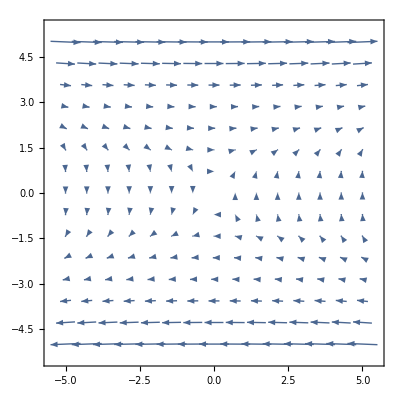

```mathematica
VectorPlot[{y^3,x},{x,-5,5},{y,-5,5}]
```

```mathematica
ClearAll["Global`*"];
r[t_]:={Cos[t],Sin[t]};
F[{x_,y_}]:={(y^3-3*x*y^2)/(y^6+x^2)};
dr=D[r[t],t]
ds=Sqrt[dr.dr]
F[r[t]].ds
NIntegrate[(-3 Cos[t] Sin[t]^2+Sin[t]^3)/(Cos[t]^2+Sin[t]^6)*√(Cos[t]^2+Sin[t]^2),{t,0,2*Pi}]
```

{-Sin[t],Cos[t]}

√(Cos[t]^2+Sin[t]^2)

{(-3 Cos[t] Sin[t]^2+Sin[t]^3)/(Cos[t]^2+Sin[t]^6)}.√(Cos[t]^2+Sin[t]^2)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.22111}. NIntegrate obtained 4.16334×10^-16 and 7.28637×10^-16 for the integral and error estimates.

4.16334×10^-16